```mathematica
test:=Series[xs*-1/Sqrt[(xt-xs)^2+y^2],{y,c,2}]
```

```mathematica
xp := Normal[test]
```

```mathematica
xp2 = xp/.{y->0}
```

(c^2 xs (-2 c^2+xs^2-2 xs xt+xt^2))/(2 (c^2+xs^2-2 xs xt+xt^2)^(5/2))-(c^2 xs)/((c^2+xs^2-2 xs xt+xt^2)^(3/2))-xs/(√(c^2+xs^2-2 xs xt+xt^2))

```mathematica
(*Plot[xp2/.xt->.4,{xs,0.35,0.45}]*)
```

```mathematica
qbx =Assuming[xt>-1,Assuming[xt<1,Assuming[c>0,Integrate[xp2,{xs,-1,1}]]]]
```

-1/(240 ((c^2+(-1+xt)^2) (c^2+(1+xt)^2))^(9/2))(70 c^16 (-3 √(c^2+(-1+xt)^2)+3 √(c^2+(1+xt)^2)-6 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-8 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+40 (-1+xt^2)^8 (-2 √(c^2+(-1+xt)^2)+2 √(c^2+(1+xt)^2)-3 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-5 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+7 c^14 (-195 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-305 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-245 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+73 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-422 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-260 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+10 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+8 c^2 (-1+xt^2)^6 (-188 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-89 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+42 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+85 (-√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-203 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-154 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+37 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+3 c^12 (-1330 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-2373 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-2765 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-1183 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+547 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-2603 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-3143 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-1505 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+147 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+c^4 (-1+xt^2)^4 (-2550 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-6135 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-5719 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-2197 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+1241 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-5809 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-6637 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-3859 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+945 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+2 c^10 (-3435 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-6225 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-6230 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-6090 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-3087 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+1515 xt^10 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-6720 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-7032 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-5880 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-4520 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+600 xt^9 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+c^6 (-1+xt^2)^2 (-5525 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-11505 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-11514 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-9882 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-5169 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+2635 xt^10 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-11990 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-11544 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-10932 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-8184 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+1690 xt^9 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+2 c^8 (-3805 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-4755 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-2354 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-2870 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-3713 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-4743 xt^10 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+1760 xt^12 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-7815 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-1873 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-2678 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-2930 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-6099 xt^9 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+915 xt^11 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))))

```mathematica
(*Plot[qbx,{xt,-1,1}]*)
```

```mathematica
qbxD=Assuming[xt>-1,Assuming[xt<1,Assuming[c>0,Simplify[D[qbx,{xt,2}]]]]]
```

1/(16 (c^2+(-1+xt)^2)^7 (c^2+(1+xt)^2)^7)(56 c^26 (-1+xt^2) (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+16 xt (-1+xt^2)^13 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)+xt (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2)))+8 c^2 xt (-1+xt^2)^11 (25 xt (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+27 xt^3 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+27 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+25 xt^2 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+28 c^24 (-9 √(c^2+(-1+xt)^2)+9 √(c^2+(1+xt)^2)+36 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+21 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-50 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+2 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+2 c^4 xt (-1+xt^2)^9 (575 xt (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+1038 xt^3 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+675 xt^5 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+675 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+1038 xt^2 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+575 xt^4 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+7 c^22 (-709 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+1093 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+417 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+33 (-√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-1036 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+192 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+76 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+c^6 xt (-1+xt^2)^7 (4025 xt (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+8757 xt^3 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+9499 xt^5 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+5175 xt^7 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+5175 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+9499 xt^2 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+8757 xt^4 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+4025 xt^6 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+c^20 (735 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-29827 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+24423 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+23023 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+9102 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-15227 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-36743 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+22127 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+2387 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+7 c^8 (-1+xt^2)^5 (5 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+1540 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+3570 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+4240 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+3553 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+1940 xt^10 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+1985 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+3928 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+4450 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+3120 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+1365 xt^9 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+c^18 (2205 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-45180 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-68390 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+124040 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+40641 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+19900 xt^10 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-18185 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-139376 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+34230 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+43400 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+6715 xt^9 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+7 c^10 (-1+xt^2)^3 (15 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+1869 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-2406 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-4374 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+3907 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+5497 xt^10 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+3684 xt^12 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+3709 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+2907 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-4238 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-474 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+3969 xt^9 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+2319 xt^11 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+c^16 (2499 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-16419 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-254762 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+137130 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+159599 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+46313 xt^10 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+32136 xt^12 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-19445 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-165579 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-183266 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+219002 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+29607 xt^9 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+13185 xt^11 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+7 c^12 (-1+xt^2) (-578 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-613 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+41128 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+18475 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-2154 xt^10 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+4085 xt^12 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+5220 xt^14 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+27 (-√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+4589 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-3286 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+19819 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+40492 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+115 xt^9 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+906 xt^11 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+2901 xt^13 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2)))+c^14 (1323 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+13928 xt^2 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-208903 xt^4 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-196086 xt^6 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+342813 xt^8 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+44564 xt^10 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+28639 xt^12 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))+39258 xt^14 (√(c^2+(-1+xt)^2)-√(c^2+(1+xt)^2))-26665 xt (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-43290 xt^3 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-374775 xt^5 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+171540 xt^7 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+189177 xt^9 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))-474 xt^11 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))+18951 xt^13 (√(c^2+(-1+xt)^2)+√(c^2+(1+xt)^2))))

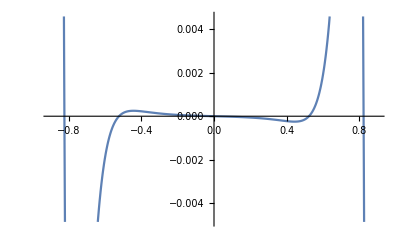

```mathematica
Plot[{qbxD/.c->1/4}+2xt,{xt,-0.9,0.9}]
```